```mathematica
homeDir=$HomeDirectory;
fdaDirectory=homeDir<>"\\Desktop\\Mathematica\\";
desktopDirectory=homeDir<>"\\Desktop\\";
pathSVM=desktopDirectory<>"SVM\\"
scriptDir=desktopDirectory<>"Scripts\\Modern\\";
SetDirectory[scriptDir]
outputDir=desktopDirectory<>"Surrogates\\Denervation\\"
nb1=fdaDirectory<>"librarySmall-header.nb";
nb=NotebookOpen[nb1];
SelectionMove[nb,All,Notebook];
SelectionEvaluate[nb];
NotebookClose[nb];
parmsAndRanges=Import[outputDir<>"parmsAndRanges.txt","CSV"];
rawvars=Import[outputDir<>"varroster.Script","Text"];
varRoster=StringSplit[StringSplit[StringReplace[rawvars,{"<roster>"->"","</roster>"->"","<var><name>"->"","\n\n"->"\n","</name>"->"","</var>"->""," "->""}],"\n"],"<format>"][[All,1]]
parmList=parmsAndRanges[[All,1]];
Ranges=parmsAndRanges[[All,2]];
p[x_,y_]:=Less[ToExpression[StringSplit[x,{".","_"}][[2]]],ToExpression[StringSplit[y,{".","_"}][[2]]]]
```

C:\Users\HL\Desktop\SVM\

C:\Users\HL\Desktop\Scripts\Modern

C:\Users\HL\Desktop\Surrogates\Denervation\

{System.X,SystemicArtys.SBP,SystemicArtys.Pressure,SystemicArtys.DBP,RightAtrium.Pressure,LeftAtrium.Pressure,CardiacOutput.Flow,CardiacOutput.StrokeVolume,Heart-Rate.Rate,BloodPhValues.ArtysPh,ECFV.Vol(L),NaPool.[Na+(mEq/L)],ANPPool.[ANP],AldoPool.[Aldo(pMol/L)],ReninPool.[PRA],A2Pool.[A2(pG/mL)]}

```mathematica
(* I am excluding the sampling and running aspects of the software suite.  Contact me if you would like them separately*)
SetDirectory[outputDir]
DataOut=ToExpression[Import[outputDir<>"denervationData.csv"]];
samples=ToExpression[Import[outputDir<>"denervationSamples.csv"]];
newsamples=samples;
```

C:\Users\HL\Desktop\Surrogates\Denervation

```mathematica
limitX={40354,40356};
limitMAP={75,200};
limitCO={2000,7000};
limitPH={6.9,7.5};
limitECFV={10,20};


limits={Interval[limitX],Interval[limitMAP],Interval[limitCO],Interval[limitPH],Interval[limitECFV]};
(*limits={Interval[limitX],Interval[limitMAP],Interval[limitCO],Interval[limitAldo],Interval[limitADH],Interval[limitANP],Interval[limitNa],Interval[limitGFR]};*)
dataout=DataOut;
FullData=Table[{newsamples[[i]],dataout[[i,1]],dataout[[i,2]]},{i,Length[dataout]}];
FullData=Select[FullData,Union[{IntervalMemberQ[limits[[1]],#[[-1,1]]],IntervalMemberQ[limits[[2]],#[[2,3]]],IntervalMemberQ[limits[[3]],#[[2,7]]],IntervalMemberQ[limits[[4]],#[[2,10]]],IntervalMemberQ[limits[[5]],#[[2,11]]]}]=={True}&];
diffList=FullData[[All,2,4]]-FullData[[All,3,4]];
fullData=Map[Flatten,Table[{FullData[[i]],{diffList[[i]]}},{i,1,Length[diffList]}]];

modeldata=FullData[[All,2;;3]];
samples=FullData[[All,1]];
newsamples=samples;
spl=parmList;

mup=Map[Mean,Transpose[samples]];
sigp=Map[StandardDeviation,Transpose[samples]];
rangeList=Transpose[{mup-2sigp,mup+2*sigp}];
```

```mathematica
indexOfInterest=3;
cList={250};
gList={.01};

For[ind1=1,ind1≤Length[cList],ind1++,
For[ind2=1,ind2≤Length[gList],ind2++,
cc=cList[[ind1]];
gg=gList[[ind2]];
generatePopulationModels[1000,indexOfInterest,modeldata,samples,varRoster,False];
Print[{cc,gg,StandardDeviation[error]}]]]
```

{250,0.01,3.46233}

```mathematica
NList={100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500}
errorList={};
For[NNN=1,NNN≤Length[NList],NNN++,
templist={};
Do[
nnn=NList[[NNN]];
cc=250;
gg=0.01;
generatePopulationModels[nnn,indexOfInterest,modeldata,newsamples,varRoster,False];
AppendTo[templist,StandardDeviation[error]],{3}];
AppendTo[errorList,templist]]
```

{100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500}

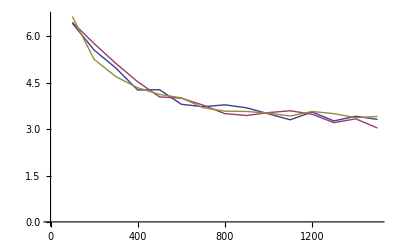

```mathematica
teL=Transpose[errorList];
hummoderrors=Transpose[Insert[teL,NList,1]];
list1=hummoderrors[[All,1;;2]];
list2=hummoderrors[[All,{1,3}]];
list3=hummoderrors[[All,{1,4}]];
ListPlot[{list1,list2,list3},Joined->True]
```

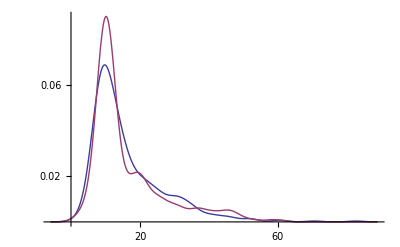

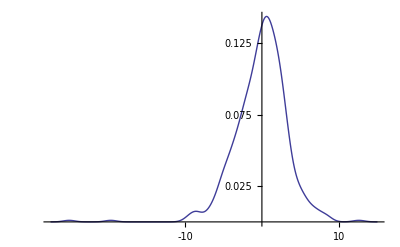

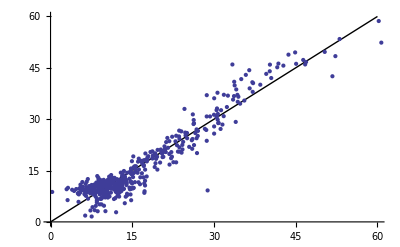

```mathematica
SmoothHistogram[{dt,loutput}]
SmoothHistogram[error]
errorData=Transpose[{dt,loutput}];
Show[Plot[x,{x,0,60},PlotStyle->{Black,Thick}],ListPlot[errorData]]
```

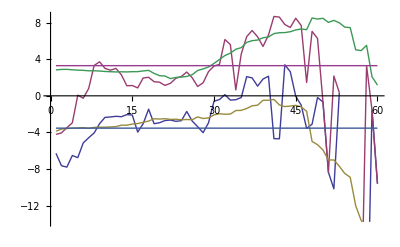

```mathematica
T=Sort[Transpose[{loutput,dt}]];

rollingWindow[x_,xi_]:=Module[{ind},
X=x[[All,1]];
m=Min[X];
M=Max[X];
window={};
For[ind=m,ind≤M,ind++,
temp=Select[x,IntervalMemberQ[Interval[{ind-xi,ind+xi}],#[[1]]]&];
dtemp=temp[[All,1]]-temp[[All,2]];
If[Length[dtemp]>1,
AppendTo[window,{Mean[dtemp],StandardDeviation[dtemp]}],
AppendTo[window,{Mean[dtemp],0}]]];
Return[window]];

view[w_]:={w[[All,1]]-w[[All,2]],w[[All,1]]+w[[All,2]]};
jList={1,10,100};
views=Table[view[rollingWindow[T,jList[[j]]]],{j,1,Length[jList]}];
ListPlot[Flatten[views,1],Joined->True]
```

```mathematica
Length[newsamples]
Length[modeldata]
```

2000

1982